```mathematica
simpson[func_,a_,b_,N_]:= Block[{h=(b-a)/N,key=Table[a+h*k,{k,1,N-1}],mid=Table[a+h/2+h*k,{k,0,N-1}]},h*(Total[func[key]]/3+2*Total[func[mid]]/3+func[a]/6+func[b]/6)];
logspace[a_,b_,num_]:=Table[10^k,{k,a,b,(b-a)/(num-1)}];
```

logspace was defined so that it reproduces the behavior of np.logspace

```mathematica
n=logspace[0,4,100];
n=Floor[n]; (* n.astype(int) *)
```

```mathematica
simpintegral=Map[simpson[Exp,0,1,#1]&,n];
simperror=simpintegral-Integrate[Exp[x],{x,0,1}];
StringForm["Precision of error: ``",Precision[simperror]]
```

Precision of error: ∞

Taking logs outside plotting function and converting to decimal number with 10 digits (instead of using ListLogLogPlot) in case the plotting function doesn’t use arbitrary precision when taking logs. Infinite precision is lost here (but after taking log) so that numbers can be plotted.

Precision of log of error: 10.

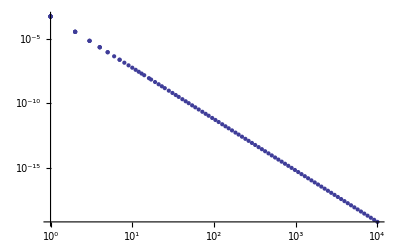

```mathematica
logsimperror=N[Log[10,simperror],10];
StringForm["Precision of log of error: ``", Precision[logsimperror]]
logn=N[Log[10,n],10];
ListPlot[Table[{logn[[k]],logsimperror[[k]]},{k,1,Length[n]}],Ticks->{Table[{k,Superscript[10,k]},{k,0,4}],Table[{k,Superscript[10,k]},{k,-25,0}]}]
```